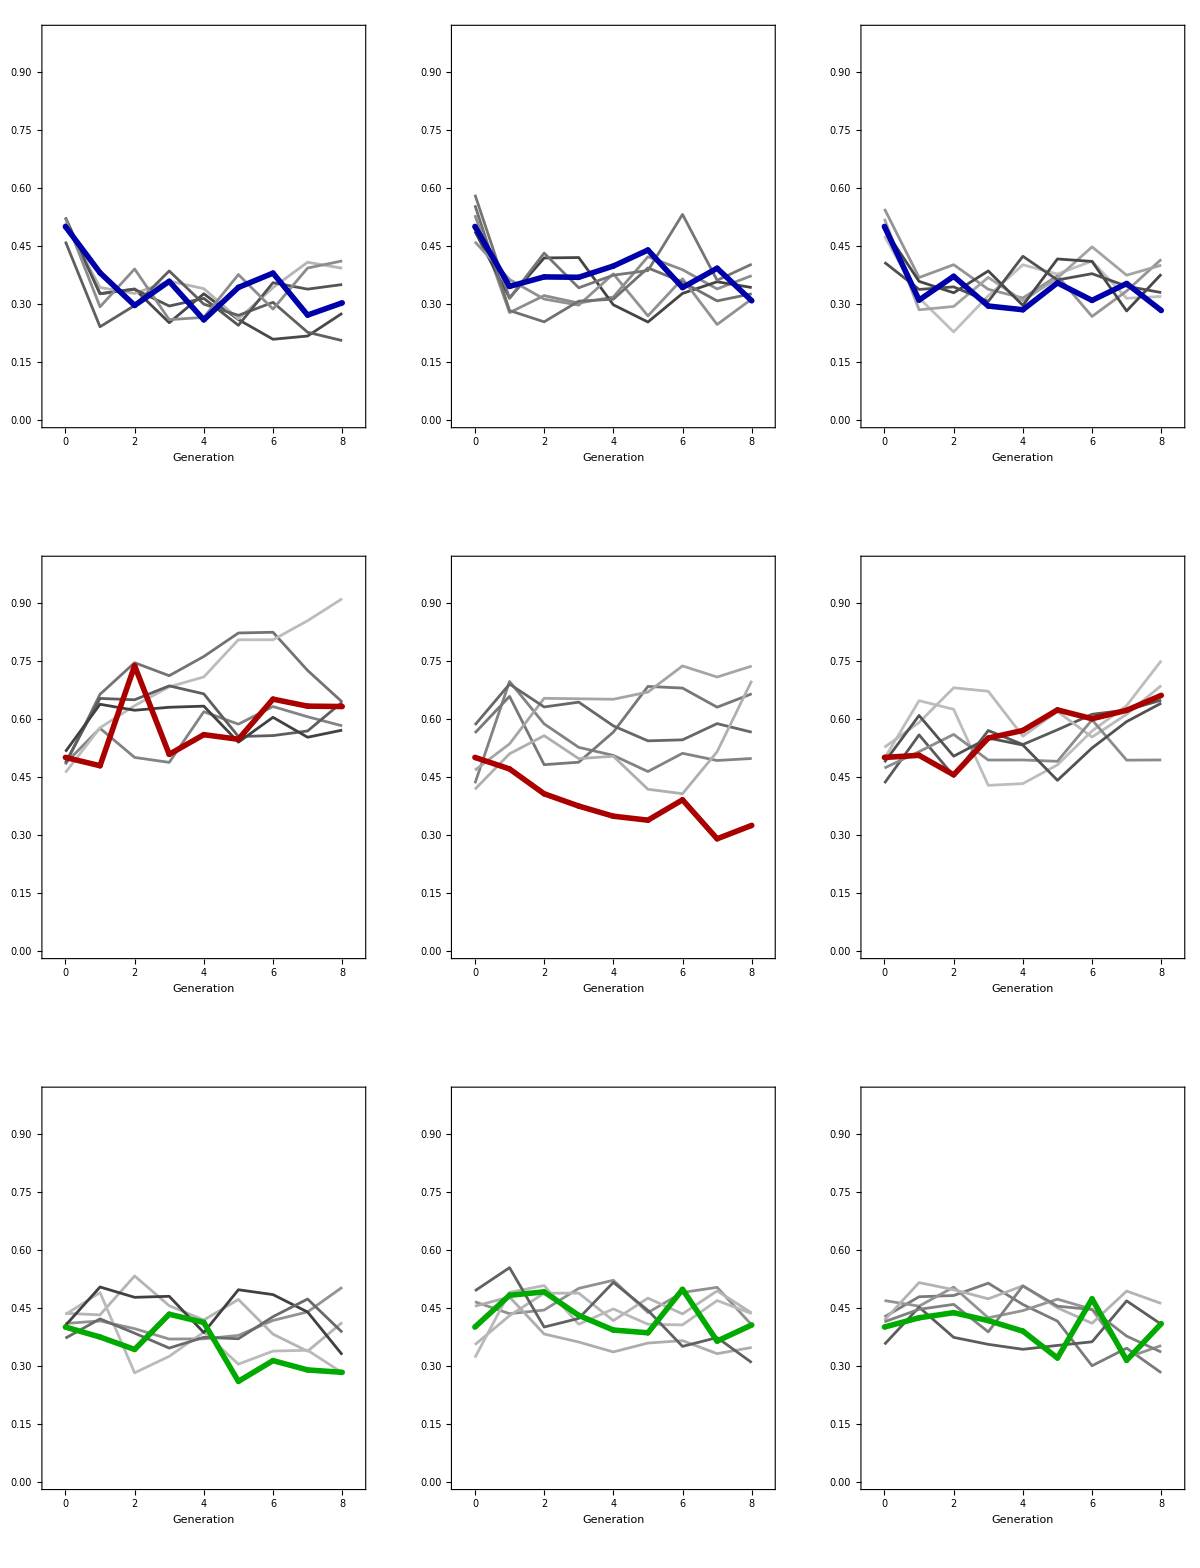

```mathematica
SetDirectory["~/Dropbox/Doublesex/qfs5/SouthKen/Nov26"];

(*Import processing functions*)
Get["SimulationProcessingFunctions.wl"];
(*set default parameters*)
parameters={(*1: Wildtype egg clutch size, θ*)100,(*2: female fitness with 1 copy of qfs5, ω_D*)0.2,(*3: female fitness with 1 copy of R2, ω_R*)1,(*4: prob a mated female lays a clutch of eggs in lifetime*)1,(*5: homing rate*)0.9,(*6: rate of creation of R from NHEJ events*)0.5,(*7: prob a female mates during lifetime*)1,(*8: number of eggs reared each generation to form next generation*)600,(*9: number of generations*)8,(*10: number of replicate simulations*)3,(*11: initial number of W/W females*)30,(*12: initial number of W/D females*)150,(*13: initial number of D/D females*)0,(*14: initial number of W/R females*)120,(*15: initial number of R/R females*)0,(*16: initial number of D/R females*)0,(*17: initial number of W/W males*)30,(*18: initial number of W/D males*)150,(*19: initial number of D/D males*)0,(*20: initial number of W/R males*)120,(*21: initial number of R/R males*)0,(*22: initial number of D/R males*)0};
(*example run with 1000 samples and acceptance fraction of 5%*)
NumberOfSamples=1000;
AcceptanceFraction=0.05;
Results=Table[GenerateParticle[parameters,pupae,1],{i,NumberOfSamples}];
quan=Quantile[Results[[All,3]],AcceptanceFraction];
Posterior=Select[Results,#[[3]]<=quan&];
GenerateDataPlot[parameters,Posterior,(*number of simulation lines to plot*)5,(*book-keeping index*)1,(*line thickness*)0.005]
```

```mathematica
femAll
```

{{{0.506579,0.310811,0.46,0.340136,0.335616,0.387097,0.326667,0.383562,0.389222},{0.509804,0.33557,0.391026,0.264901,0.366667,0.392638,0.294118,0.312102,0.377358},{0.456954,0.434483,0.360544,0.283688,0.298013,0.307692,0.283951,0.273973,0.426752}},{{0.442177,0.414966,0.296053,0.25974,0.224359,0.2,0.22695,0.226667,0.230769},{0.442177,0.333333,0.298611,0.348101,0.357616,0.270833,0.345324,0.355705,0.228758},{0.486486,0.364238,0.221477,0.409396,0.240506,0.284768,0.308219,0.22,0.281879}},{{0.472441,0.261194,0.282609,0.301471,0.25,0.208333,0.213235,0.251852,0.195652},{0.514706,0.40458,0.340741,0.277372,0.376923,0.34507,0.284615,0.313433,0.316176},{0.507353,0.268657,0.276923,0.29927,0.285714,0.181818,0.283688,0.230263,0.231293}},{{0.454545,0.277311,0.297297,0.316176,0.333333,0.344,0.389706,0.302521,0.281481},{0.507813,0.281481,0.291971,0.315385,0.310078,0.322835,0.282258,0.285714,0.402985},{0.525926,0.315436,0.357664,0.307692,0.366412,0.294118,0.380597,0.384,0.39823}},{{0.52027,0.30137,0.339394,0.366013,0.304965,0.360759,0.34,0.363014,0.383562},{0.455172,0.268456,0.368421,0.351351,0.313725,0.350649,0.310811,0.344595,0.344595},{0.467949,0.274648,0.401361,0.396226,0.350318,0.341772,0.406667,0.477707,0.416667}}}